```mathematica
eqn = 1==(0.60 *Exp[9.2131-2477.07/(T-39.94)])+(0.40*Exp[9.2164-2697.07/(T-48.78)])
FindRoot[eqn,{T,300}]
Manipulate[(0.60 *Exp[9.2131-2477.07/(T-39.94)])+(0.40*Exp[9.2164-2697.07/(T-48.78)]),{T,0,400}]
eqn1 = 1== 1/(0.6/Exp[9.2131-2477.07/(T-39.94)]+0.4/Exp[9.2164-2697.07/(T-48.78)])
FindRoot[eqn1,{T,300}]
FindRoot[1/(y/Exp[9.2131-2477.07/(318.208-39.94)]+(1-y)/Exp[9.2164-2697.07/(318.208-48.78)])== 1, {y,0}]
```

1==0.4 ⅇ^(9.2164-2697.07/(-48.78+T))+0.6 ⅇ^(9.2131-2477.07/(-39.94+T))

{T→318.208}

1==1/(0.4 ⅇ^(-9.2164+2697.07/(-48.78+T))+0.6 ⅇ^(-9.2131+2477.07/(-39.94+T)))

{T→326.377}

{y→0.819185}

```mathematica
De = 2.8*10^-11
t= 90000
Solve[1-Erf[(2.0*10^-3)/(2*Sqrt[De*t])]== Subscript[C, x]/0.2, Subscript[C, x]]
```

2.8×10^-11

90000

{{C_x→0.0745997}}

```mathematica
Binomial[3,2]/Binomial[50,3]
```

3/19600

```mathematica
Clear[x1]
x2 = 1-x1
G = A*x1*x2^2
Expand[2*A*x1^2*x2]
Expand[G-x1*D[G,x1]]
```

1-x1

A (1-x1)^2 x1

2 A x1^2-2 A x1^3

2 A x1^2-2 A x1^3

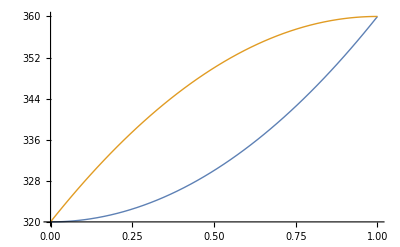

```mathematica
Plot[{320+40 x^2, 320+40x(2-x)},{x,0,1}, PlotStyle->Thick]
```

```mathematica
Solve[320+40 x^2== 320+40*0.43(2-0.43)]
```

{{x→-0.821645},{x→0.821645}}

```mathematica
Solve[1.0086(y/(0.7434*1.137)+(1-y)/(1.0324*1.152))== 1]
```

{{y→0.440173}}

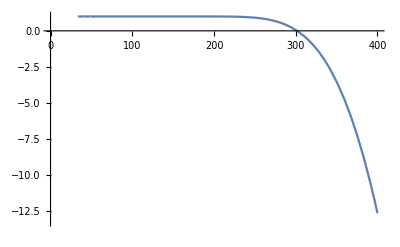

{T→301.529}

{T→276.487}

```mathematica
Plot[1 ==  1/(0.25/Exp[9.0580-2154.90/(T-34.42)]+0.35/Exp[8.9179-2032.73/(T-33.15)]+0.30/Exp[9.2131-2477.07/(T-39.94)]+0.10/Exp[9.2164-2697.07/(T-48.78)]),{T,0,400}]
FindRoot[1 ==  1/(0.25/Exp[9.0580-2154.90/(T-34.42)]+0.35/Exp[8.9179-2032.73/(T-33.15)]+0.30/Exp[9.2131-2477.07/(T-39.94)]+0.10/Exp[9.2164-2697.07/(T-48.78)]),{T,400}]
FindRoot[1== 0.25*Exp[9.0580-2154.90/(T-34.42)]+0.35*Exp[8.9179-2032.73/(T-33.15)]+0.30*Exp[9.2131-2477.07/(T-39.94)]+0.10*Exp[9.2164-2697.07/(T-48.78)],{T,200}]
```

```mathematica
0.5*Exp[9.2164-2697.07/(370-48.78)]+0.5*Exp[9.2535-2911.32/(370-56.51)]
```

1.61895

```mathematica
Solve[0.80==  0.5 Subscript[y, 1]+0.5 Subscript[x, 1],Subscript[y, 1]]
```

2 (0.8-0.5 x_1)

{}

```mathematica
Subscript[y, 1]=2 (0.8-0.5 Subscript[x, 1])
Simplify[0.20== 0.5(1-Subscript[y, 1])+0.5(1-Subscript[x, 1])]
```

2 (0.8-0.5 x_1)

True